## Constructing graphs using edges

```mathematica
g=Graph[{DirectedEdge[1,2],UndirectedEdge[1,3],UndirectedEdge[3,2]},ImageSize->120]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges.pdf

```mathematica
g=Graph[{Style[1->2,Thick,Red],Style[1<->3,Dashed],3<->2},ImageSize->120]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges-style.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges-style.pdf

```mathematica
g=Graph[g,VertexSize->Small,VertexLabels->"Name"]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges-style-vertices.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges-style-vertices.pdf

```mathematica
g=Graph[g,VertexSize->Small,VertexLabels-> {_->"Name",2->Placed["Name",After]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges-style-vertices-fixed-after.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges-style-vertices-fixed-after.pdf

```mathematica
Graph[g,VertexSize->Small,VertexLabels-> 2->Placed["Name",{2.5,1.5}]]
```

-Graphics-

```mathematica
Table[g=Graph[g,VertexSize->Small,VertexLabels-> 2->Placed["Name",p]],{p,{Before,Above,{2.5,1.5}}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges-style-vertices-fixed.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges-style-vertices-fixed.pdf

```mathematica
g=Graph[g,VertexLabels->{3->"Here!"},VertexSize->{3->Medium}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-individual-style.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-individual-style.pdf

```mathematica
Graph[{DirectedEdge[1,2],UndirectedEdge[1,3],UndirectedEdge[3,2]},VertexSize->Medium, VertexLabels->"Name",ImageSize->120]
```

-Graphics-

```mathematica
Graph[{Style[DirectedEdge[1,2],Thick, Red],Style[UndirectedEdge[1,3],Dashed],UndirectedEdge[3,2]},
VertexSize->Small, VertexLabels->"Name",ImageSize->120]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-graph-edges-2.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-graph-edges-2.pdf

## Adjacency matrix

```mathematica
ag=AdjacencyGraph[{{0,1,0},{1,0,1},{1,1,0}},DirectedEdges->Automatic,ImageSize->120,VertexLabels->{_->"Name",1->Placed["Name",{3,-1}]},VertexLabelStyle->Directive[Red,Italic,12]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-adjacency-graph.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-adjacency-graph.pdf

```mathematica
AdjacencyMatrix[ag]//Normal
```

{{0,1,0},{1,0,1},{1,1,0}}

```mathematica
agud=AdjacencyGraph[{{0,1,1},{1,0,1},{1,1,0}},DirectedEdges->Automatic,ImageSize->120,VertexLabels->{_->"Name",1->Placed["Name",{-1,4.5}]},VertexLabelStyle->Directive[Red,Italic,12]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-adjacency-graph-undirected.pdf",agud]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-adjacency-graph-undirected.pdf

## Graph constructing functions

```mathematica
PathGraph[Range[20],PlotLabel->Subscript[P, 20] ,VertexSize->Medium,ImageSize->130]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-path-graph.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-path-graph.pdf

```mathematica
CompleteGraph[7,PlotLabel->Subscript[K, 7],
VertexSize->0.25,
 VertexShapeFunction->"Square",
ImageSize->130]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-complete-graph.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-complete-graph.pdf

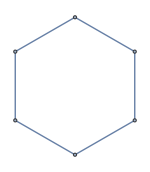

```mathematica
CycleGraph[6,ImageSize->150]
```

```mathematica
cg=CycleGraph[7,PlotLabel->Subscript[C, 7],ImageSize->130,DirectedEdges->True,EdgeStyle->Arrowheads[Large],EdgeLabels->{1->2->Placed[Subscript[a, 12],{Left,"Middle"}]},
EdgeLabelStyle->Directive[Blue,Bold,12]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/02-cycle-graph.pdf",cg]
```

/home/jam/Kuweta/mma_lessons/code/pics/02-cycle-graph.pdf

```mathematica
CycleGraph[5,
DirectedEdges->False,
EdgeStyle->Arrowheads[Large],
EdgeLabels->{1<->2->"a_12"},
ImageSize->130]
```

-Graphics-

```mathematica
CycleGraph[5,
DirectedEdges->True,
EdgeStyle->Arrowheads[Large],
EdgeLabels->{1->2->Placed["a_12",{Left,"Middle"}]},
ImageSize->130]
```

-Graphics-

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 1
0 | 0 | 1
1 | 1 | 0)

## Elements of the graphs

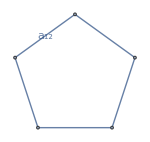

```mathematica
g=CycleGraph[5,
DirectedEdges->False,
EdgeStyle->Arrowheads[Large],
EdgeLabels->{1<->2->"a_12"},
ImageSize->150]
```

```mathematica
VertexList[g]
```

{1,2,3,4,5}

```mathematica
EdgeList[g]
```

{1<->2,1<->5,2<->3,3<->4,4<->5}

## Layouts

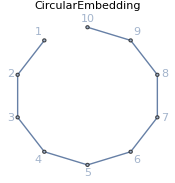
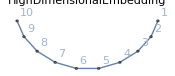
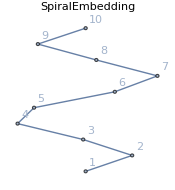
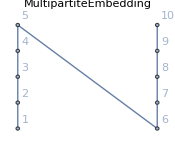
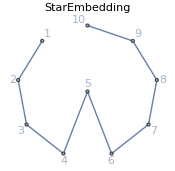
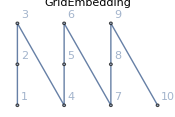

```mathematica
Table[PathGraph[Range[10],ImageSize->175,PlotLabel->l,VertexLabels->"Name",GraphLayout->l],{l,{"CircularEmbedding","HighDimensionalEmbedding","SpiralEmbedding","MultipartiteEmbedding","StarEmbedding","GridEmbedding"}}]
```

```mathematica
Table[Export[NotebookDirectory[]<>"pics/02-graph-layout-"<>ToString[l]<>".pdf",PathGraph[Range[10],GraphLayout->l,PlotLabel->l,ImageSize->152,VertexLabels->"Name"]],{l,{"CircularEmbedding","StarEmbedding","SpiralEmbedding","MultipartiteEmbedding","HighDimensionalEmbedding","GridEmbedding"}}]
```

{/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-CircularEmbedding.pdf,/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-StarEmbedding.pdf,/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-SpiralEmbedding.pdf,/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-MultipartiteEmbedding.pdf,/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-HighDimensionalEmbedding.pdf,/home/jam/Kuweta/mma_lessons/code/pics/02-graph-layout-GridEmbedding.pdf}

## Weighted graphs

```mathematica
Clear[wg,g]
```

```mathematica
edges={1->2,2->3,3->4,4->2,5->2};
```

```mathematica
wg=Graph[edges,EdgeWeight->{_?(OddQ[First[#]]&)-> -1}];
```

```mathematica
AnnotationValue[wg, EdgeWeight]
```

{-1,1,-1,1,-1}

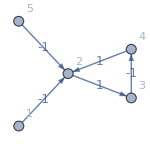

```mathematica
Graph[wg,EdgeLabels->"EdgeWeight",
VertexLabels->"Name",
VertexSize->Medium, 
EdgeLabelStyle->Directive[12],
ImageSize->150]
```

```mathematica
Export[NotebookDirectory[]<>"pics/05-weighted-graph.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/05-weighted-graph.pdf

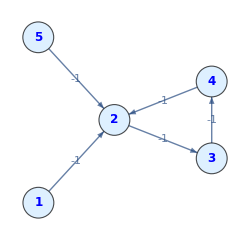

```mathematica
Graph[wg,
EdgeLabels->Framed[
AnnotationValue[{wg,#},EdgeWeight],
Background->White,
RoundingRadius->2,
ImageSize->{25,25},
Alignment->Center
]&/@EdgeList[wg],
EdgeLabelStyle->Directive[11],
VertexLabels->Placed["Name",Center],
VertexLabelStyle->Directive[Blue,Bold,12],
VertexSize->Large,
VertexStyle->LightBlue,
ImageSize->250]
```

```mathematica
Export[NotebookDirectory[]<>"pics/05-weighted-graph-improved.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/05-weighted-graph-improved.pdf

```mathematica
AnnotationValue[{wg,#},EdgeWeight]&[1->2]
```

-1

## Random graphs

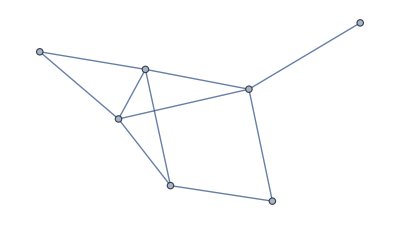

```mathematica
g=RandomGraph[{7,10}]
```

```mathematica
Graph[g,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

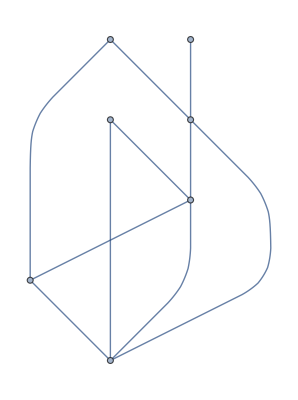

```mathematica
Graph[g,GraphLayout->"LayeredDigraphEmbedding"]
```

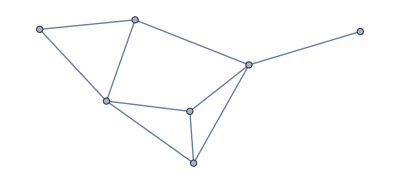

```mathematica
g=RandomGraph[{7,10}]
```

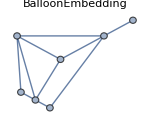
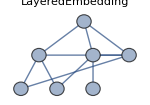
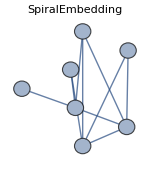
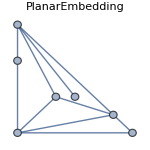
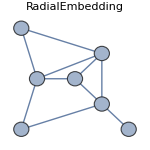
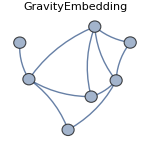

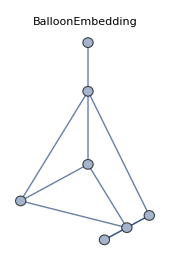
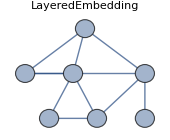

```mathematica
g=RandomGraph[{7,10}];
Table[Graph[g,GraphLayout->l,PlotLabel->l,ImageSize->150,VertexSize->Large],{l,{"BalloonEmbedding","LayeredEmbedding","SpiralEmbedding","PlanarEmbedding","RadialEmbedding","GravityEmbedding"}}]
```

```mathematica
Table[Export[NotebookDirectory[]<>"pics/05-random-graph-layout-"<>l<>".pdf",g=Graph[g,GraphLayout->l,PlotLabel->l,ImageSize->150,VertexSize->Large]];g,{l,{"BalloonEmbedding","LayeredEmbedding","SpiralEmbedding","PlanarEmbedding","RadialEmbedding","GravityEmbedding"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Random graphs

```mathematica
styles={Red,Blue,Green,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],GrayLevel[0]}

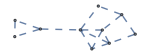
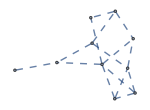
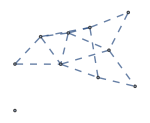
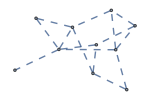

```mathematica
g=Table[
RandomGraph[{10,15},ImageSize->150,EdgeStyle->Directive[Dashed]],{i,1,4}]
```

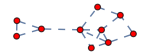
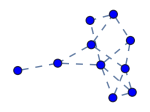
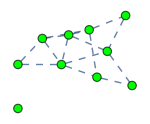
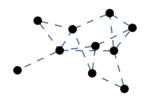

```mathematica
sg=Table[Graph[g[[i]],VertexSize->Large,VertexStyle->styles[[i]]],{i,1,4}]
```

```mathematica
Table[
Export[
NotebookDirectory[]<>"pics/05-random-graph-"<>ToString[i]<>".pdf",Graph[g[[i]],VertexSize->Large,VertexStyle->styles[[i]]]],{i,1,4}]
```

{/home/jam/Kuweta/mma_lessons/code/pics/05-random-graph-1.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-random-graph-2.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-random-graph-3.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-random-graph-4.pdf}

### Watts-Strogatz distribution

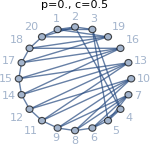
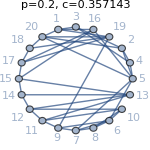
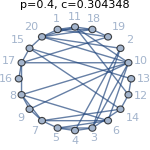
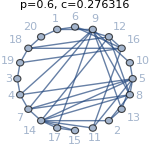
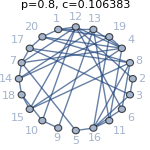
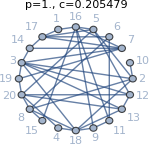

```mathematica
probs=Table[i/100.,{i,0,100,20}];
wsg=Table[
RandomGraph[WattsStrogatzGraphDistribution[20,p]],{p,probs}
];
wsg=Table[Graph[wsg[[i]],GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->150,VertexSize->Large,PlotLabel->"p="<>ToString[probs[[i]]]<>", c="<>ToString[N[GlobalClusteringCoefficient[wsg[[i]]]]]],{i,1,Length[wsg]}]
```

```mathematica
Table[Export[NotebookDirectory[]<>"pics/05-ws-graph-"<>ToString[i]<>".pdf",wsg[[i]]],{i,1,Length[wsg]}]
```

{/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-1.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-2.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-3.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-4.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-5.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ws-graph-6.pdf}

### Barabasi-Albert distribution

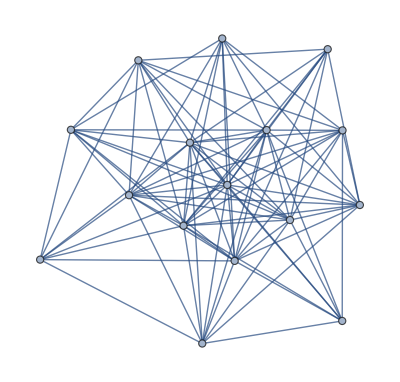

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[16,8]]
```

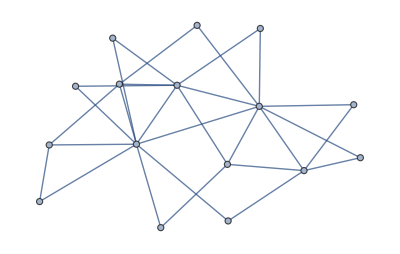
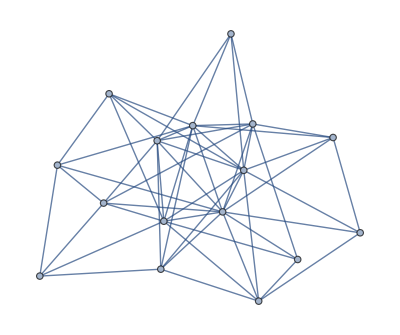
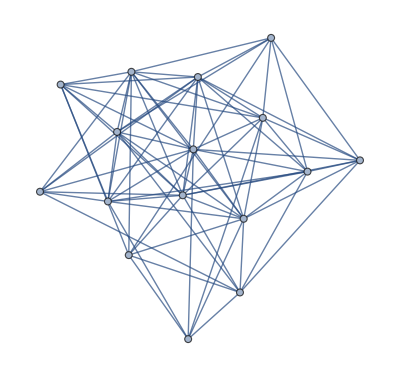
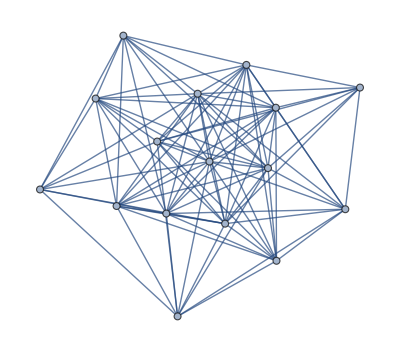
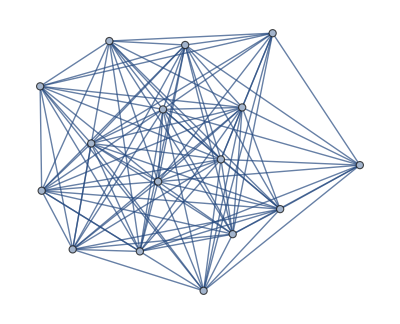
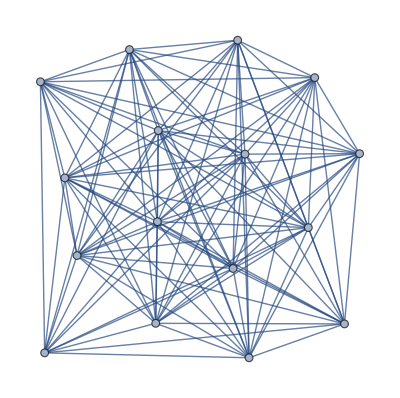
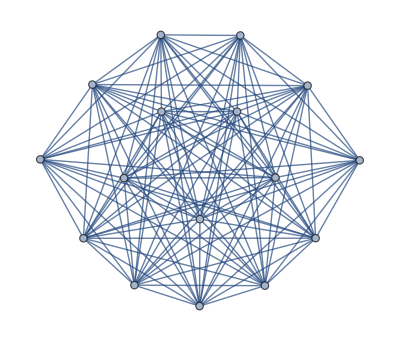
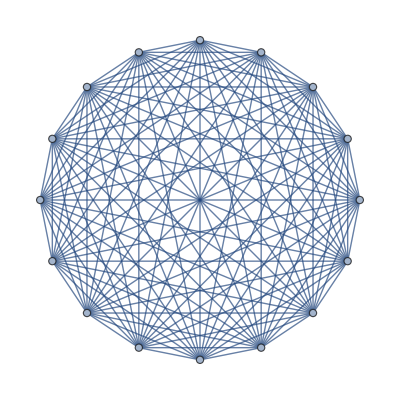

```mathematica
Table[RandomGraph[BarabasiAlbertGraphDistribution[16,2 i]],{i,1,8}]
```

```mathematica
Table[g=RandomGraph[BarabasiAlbertGraphDistribution[16,2 i],VertexSize->Large];Export[NotebookDirectory[]<>"pics/05-ba-graph-"<>ToString[i]<>".pdf",g],{i,1,8}]
```

{/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-1.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-2.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-3.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-4.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-5.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-6.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-7.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-ba-graph-8.pdf}

## Graph algorithms

### FindHamiltonianCycle

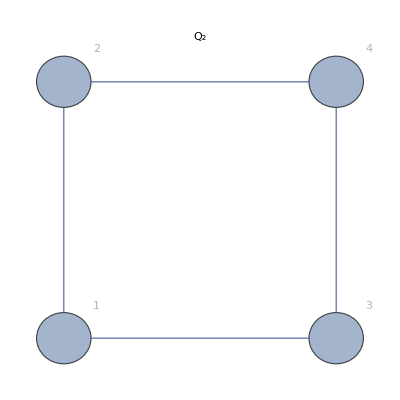
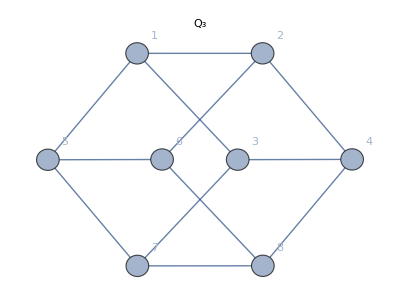
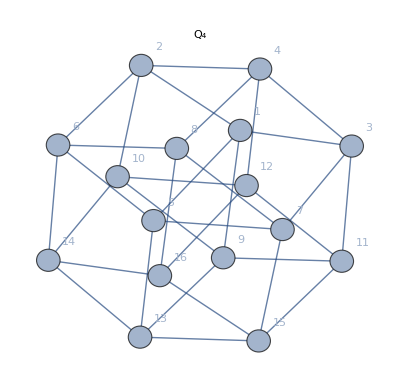
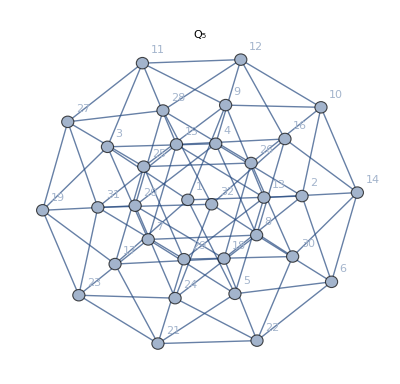

```mathematica
Table[HypercubeGraph[i,PlotLabel->Subscript[Q, i],VertexLabels->"Name",VertexSize->i/10],{i,2,5}]
```

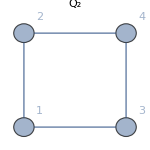
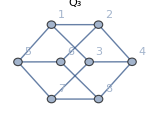
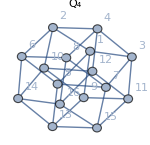
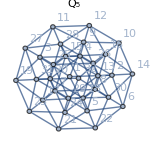

cubes

```mathematica
Clear[cubes];
Table[cubes[i]=HypercubeGraph[i,PlotLabel->Subscript[Q, i],VertexLabels->"Name",VertexSize->i/10,ImageSize->150];cubes[i],{i,2,5}]
HamiltonianGraphQ[#]&/@cubes
```

```mathematica
(hamCyc[#]=FindHamiltonianCycle[cubes[#]])&/@Range[2,5]
```

{{{1<->2,2<->4,4<->3,3<->1}},{{1<->2,2<->4,4<->8,8<->6,6<->5,5<->7,7<->3,3<->1}},{{1<->2,2<->4,4<->8,8<->16,16<->12,12<->11,11<->3,3<->7,7<->15,15<->13,13<->5,5<->6,6<->14,14<->10,10<->9,9<->1}},{{1<->5,5<->21,21<->23,23<->7,7<->3,3<->19,19<->27,27<->11,11<->12,12<->10,10<->26,26<->28,28<->32,32<->16,16<->14,14<->6,6<->2,2<->18,18<->20,20<->4,4<->8,8<->24,24<->22,22<->30,30<->29,29<->31,31<->15,15<->13,13<->9,9<->25,25<->17,17<->1}}}

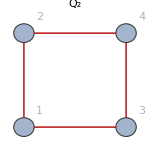
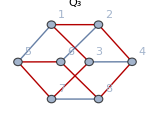
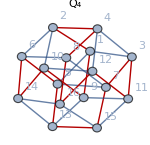
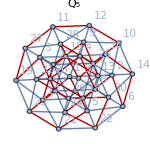

```mathematica
HighlightGraph[cubes[#],First[hamCyc[#]],GraphHighlightStyle->"Thick"]&/@Range[2,5]
```

```mathematica
Export[NotebookDirectory[]<>"pics/05-hamcycle-qighlight-q"<>ToString[#]<>".pdf",HighlightGraph[cubes[#],First[hamCyc[#]],GraphHighlightStyle->"Thick"]
]&/@Range[2,5]
```

{/home/jam/Kuweta/mma_lessons/code/pics/05-hamcycle-qighlight-q2.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-hamcycle-qighlight-q3.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-hamcycle-qighlight-q4.pdf,/home/jam/Kuweta/mma_lessons/code/pics/05-hamcycle-qighlight-q5.pdf}

### FindGraphCommunities

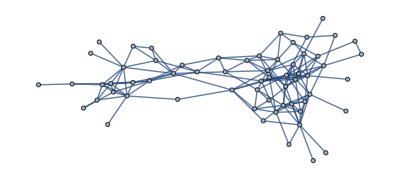

```mathematica
d=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}]
```

```mathematica
Export[NotebookDirectory[]<>"pics/05-dolphin-social-network.pdf",d]
```

/home/jam/Kuweta/mma_lessons/code/pics/05-dolphin-social-network.pdf

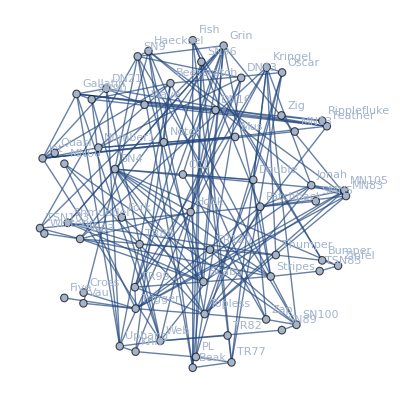

```mathematica
Graph[d,VertexLabels->"Name",ImageSize->400,GraphLayout->"SpiralEmbedding"]
```

```mathematica
commCentrality=CommunityGraphPlot[d,VertexLabels->"Name",Method->"Centrality",ImageSize->400,PlotLabel->"Method: Centrality"]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/05-community-graph-centrality.pdf",commCentrality]
```

/home/jam/Kuweta/mma_lessons/code/pics/05-community-graph-centrality.pdf

```mathematica
commuHierarchical=CommunityGraphPlot[d,VertexLabels->"Name",Method->"Hierarchical",ImageSize->350,PlotLabel->"Method: Hierarchical"]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/05-community-graph-hierarchical.pdf",commuHierarchical]
```

/home/jam/Kuweta/mma_lessons/code/pics/05-community-graph-hierarchical.pdf

```mathematica
FindGraphCommunities[d,Method->"Modularity"]
```

{{Beak,Bumper,Fish,Fork,Grin,Hook,Kringel,Scabs,Shmuddel,SN4,SN63,SN9,SN96,Stripes,Thumper,TR120,TR77,TR88,TR99,TSN103,TSN83,Whitetip,Zipfel},{Beescratch,DN16,DN21,DN63,Feather,Gallatin,Jet,Knit,MN23,Mus,Notch,Number1,Oscar,PL,Quasi,Ripplefluke,SN90,TR82,Upbang,Wave,Web,Zig},{CCL,Cross,Double,Five,Haecksel,Jonah,MN105,MN60,MN83,Patchback,SMN5,Topless,Trigger,Vau,Zap},{SN100,SN89}}

```mathematica
FindGraphCommunities[d,Method->"Centrality"]
```

{{Beescratch,DN16,DN21,DN63,Feather,Gallatin,Jet,Knit,MN23,Mus,Notch,Number1,Quasi,Ripplefluke,SN89,SN90,TR82,Upbang,Wave,Web,Zig},{CCL,Double,Fork,Grin,Hook,Kringel,Scabs,Shmuddel,SN100,SN4,SN63,SN9,Stripes,Thumper,TR120,TR88,TR99,TSN103,Whitetip,Zap},{Cross,Five,Haecksel,Jonah,MN105,MN60,MN83,Patchback,SMN5,Topless,Trigger,Vau},{Beak,Bumper,Fish,Oscar,PL,SN96,TR77},{TSN83,Zipfel}}

```mathematica
FindGraphCommunities[d,Method->"Hierarchical"]
```

{{CCL,Double,Fork,Grin,Hook,Kringel,Scabs,Shmuddel,SMN5,SN100,SN4,SN63,SN9,Stripes,Thumper,TR99,TSN103,Whitetip,Zap,Zipfel},{Beescratch,DN16,DN21,Feather,Gallatin,Jet,MN23,Mus,Notch,Number1,Quasi,Ripplefluke,SN89,SN90,TR82,Upbang,Wave,Web},{Cross,Five,Haecksel,Jonah,MN105,MN60,MN83,Patchback,Topless,Trigger,Vau},{Beak,Bumper,DN63,Fish,Knit,Oscar,PL,SN96,TR77},{TR120,TSN83},{TR88},{Zig}}